Project 11 - Power Series
Jacob Schnoor

Problem 1

```mathematica
Series[E^(I*θ),{θ,0,10}]
Series[Cos[θ],{θ,0,10}]+Series[I*Sin[θ],{θ,0,10}]
```

1+ⅈ θ-θ^2/2-(ⅈ θ^3)/6+θ^4/24+(ⅈ θ^5)/120-θ^6/720-(ⅈ θ^7)/5040+θ^8/40320+(ⅈ θ^9)/362880-θ^10/3628800+O[θ]^11

1+ⅈ θ-θ^2/2-(ⅈ θ^3)/6+θ^4/24+(ⅈ θ^5)/120-θ^6/720-(ⅈ θ^7)/5040+θ^8/40320+(ⅈ θ^9)/362880-θ^10/3628800+O[θ]^11

Problem 2

```mathematica
Series[Log[x],{x,1,4}]
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+O[x-1]^5

Ln(0) has no solution meaning a power series cannot accurately estimate the result at x=0

Problem 3

```mathematica
logXatTwo=Normal[Series[Log[x],{x,-1,10}]]/.{x-> -1}
Log[-1]
```

ⅈ π

ⅈ π

The answer is correct because if ln(y)=x, then ⅇ^x=y. According to the power series from problem 1, ⅇ^ⅈθ=Cos[θ]+ⅈSin[θ]. Plugging in π for θ results in e^ⅈπ=Cos[π]+iSin[π]= -1. Therefore ln(-1)=ⅈπ

Problem 4

```mathematica
Normal[Series[Log[x],{x,1,4}]]
Normal[Series[Log[x],{x,1,4}]]/.{x-> -1}
```

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+x

-32/3

The approximation for ln(-1) centered around x=1 is different than the previous approximation because power series have only a limited range of accuracy. As a point gets further from the center, the power series becomes less accurate. Putting the center at x=1 and evaluating ln(-1) gives -32/3 rather than ⅈπ because the polynomial above can only output real answers.

Problem 5

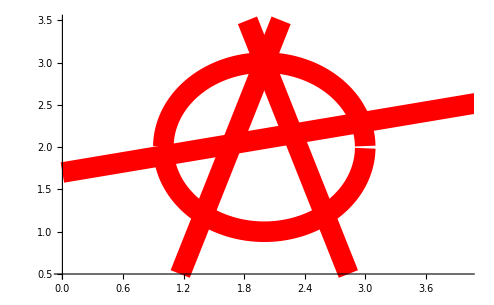

```mathematica
myMat={{0.2x+1.7},{-3x+9},{3x-3},{2-√(1-(x-2)^2)},{2+√(1-(x-2)^2)}};
Plot[myMat,{x,0,6},PlotRange->{{0,4},{0.5,3.5}},PlotStyle->{{Thickness[0.03],Red}}]
```